# Artillery Aim Simulator

## Collin Davis and Chandler Jensen

## General Information:

I believe the easiest way to go about this project is to pick an artillery weapon currently in use by the United States military and use it for our simulation. Perhaps if we were to continue the project beyond the class we could add different weapons and allow the user to pick, but let’s not get ahead of ourselves.

Wikipedia has some good info on different artillery weapons, I think the M777 Howitzer is a good choice, coupled with the 155mm M795 shell. It has the following specifications (according to Wikipedia):
Range of Elevation: 0° - +71.7°
Muzzle Velocity: 827 m/s
Effective Firing Range: 22.5km

## Global Variables:

```mathematica
V0=827; (* V0 is the initial velocity of the shell *)
maxRange=22500; (* maximum range of the cannon *)
elevationMin=0Degree; (* minimum angle between horizontal plane and cannon *)
elevationMax=71.7Degree; (* maximum angle between horizontal plane and cannon *)
ag=-9.8;(*this is the accelotration of gravity*)
```

## Artillery Simulation

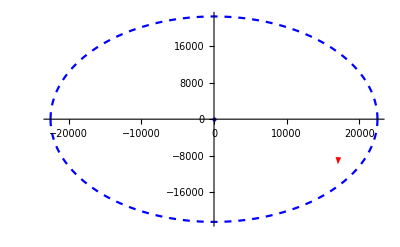

Target Position is:

{17053.7,-9880.02}

Target Speed is:

7.69136 m/s

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{329.437,0.1438}

Angles Needed Are:

AutoAim[{17053.7,-9880.02}]

Set::write: Tag Plus in -22496.8+22496.8 is Protected.

-Graphics3D-

```mathematica
(* Target Location Generation *)
rangePlot=Plot[{y=Sqrt[maxRange^2-x^2],y=-Sqrt[maxRange^2-x^2]},{x,-maxRange,maxRange},PlotRange->All,PlotStyle->{{Blue,Dashed},{Blue,Dashed}}];
targetPosition={RandomReal[{-maxRange,maxRange}],RandomReal[{-maxRange,maxRange}]} ;
While[targetPosition[[1]]^2+targetPosition[[2]]^2>maxRange^2,targetPosition={RandomReal[{-maxRange,maxRange}],RandomReal[{-maxRange,maxRange}]}]
targetX=targetPosition[[1]];
targetY=targetPosition[[2]];
artilleryPosition={0,0};
artilleryPoint=Graphics[{Blue,PointSize[Large],Point[{0,0}]}];

(* Target Movement Generation *)
targetSpeed=RandomReal[{0,35}]; (* I put 35 m/s as max speed as that is nearly 80 mph *)
targetDirection=RandomReal[{0,2π}];
targetVector=AngleVector[{targetSpeed,targetDirection}];
targetArrow=Graphics[{Arrowheads[0.05],Red,Arrow[{targetPosition,targetPosition+targetVector}]}];

(* Conditions Plot and Output *)
Show[rangePlot,targetArrow,artilleryPoint]
"Target Position is:"
targetPosition
"Target Speed is:"
targetSpeed "m/s"

(* Aiming *)
AutoAim[{{xposition_,yposition_},{targetSpeed_,targetDirection_}}]:=Module[{direction,angle,dxyf,dx=xposition,dy=yposition,az=ag,vxy0=V0 Cos[θ],
vz0=V0 Sin[θ],vy=targetSpeed Sin[targetDirection],
vx=targetSpeed Cos[targetDirection],dyf,dxf},
solvefun=Solve[(√((dy+vy t)^2+(dx+vx t)^2))/vxy0==-2 vz0/ag==t,{t,θ}];(*this is telling the time the shot is in the air at each angle we shoot*)
tt=t/.solvefun[[3]];
angle=θ/.solvefun[[3]];(*this is the Angle at which it shoots in degrees*)
dxf=dx+vx tt;
dyf=dy +vy tt;
dxyf=√(dxf^2+dyf^2)(*the distance to the point*);
If[0<=dyf/dxyf ,If[0<=dxf/dxyf,direction=(ArcTan[dyf/dxf]180)/π,direction=(ArcTan[dyf/dxf]180)/π+180],If[0<=dxf/dxyf,direction=(ArcTan[dyf/dxf]180)/π+360,direction=(ArcTan[dyf/dxf]180)/π+180]]
;(*the direction that we will shoot in degrees*)
Shotplot=ParametricPlot3D[{ dxf/tt t, dyf/tt t,V0 Sin[angle] t+1/2 az t^2},{t,0,tt},PlotRange->All];(*this is the graph for the shot*)
AimAngle={direction,angle}]
(*this is the direction and angle to hit a moving target if there is no air resistance or wind which is in the form {direction in degrees,angle in degrees}*)
AutoAim[{targetPosition,{targetSpeed,targetDirection}}]
"Angles Needed Are:"
AutoAim[targetPosition]
targetPos3D={targetPosition[[1]],targetPosition[[2]],1};
targetVec3D={targetVector[[1]],targetVector[[2]],0};
field=Plot3D[x-y=0,{x,-maxRange,maxRange},{y,-maxRange,maxRange},PlotRange->{0,1000},PlotStyle->GrayLevel[0.9,0.73]];
targetPoint3D=Graphics3D[Arrow[{targetPos3D,targetPos3D+targetVec3D}]];

Show[field,Shotplot,targetPoint3D]
```